```mathematica
VectorPlot[{-2y*x,x},{x,-3,3},{y,-3,3}]
```

```mathematica
Manipulate[Show[{ListPlot[Table[{a*x+b*y,c*x+d*y},{x,-3,3,1},{y,-3,3,1}],PlotRange->{{-7,7},{-7,7}}],ListPlot[Table[{x,y},{x,-3,3,1},{y,-3,3,1}],PlotStyle->PointSize[0.008]]}],{a,-1,1,1},{b,-1,1,1},{c,-1,1,1},{d,-1,1,1}]
```

```mathematica
StreamPlot
```

```mathematica
Manipulate[ListVectorPlot[Partition[Partition[Table[{{x,y},{(a*x+b*y)-x,(c*x+d*y)-y}},{x,-3,3},{y,-3,3}]//Flatten,2],2],PlotRange->{{-6,6},{-6,6}}],{a,-5,5,1},{b,-5,5,1},{c,-5,5,1},{d,-5,5,1}]
```

```mathematica
Partition[Partition[Table[{{x,y},{(a*x+b*y)-x,(c*x+d*y)-y}},{x,-3,3},{y,-3,3}]//Flatten,2],2]
```

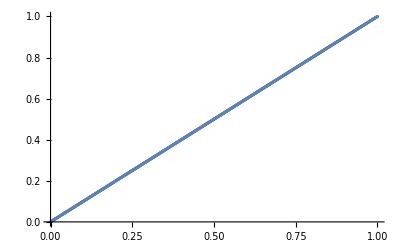

```mathematica
ListPlot[Table[{x,x},{x,0,1,0.001}]]
```

```mathematica
Manipulate[{Show[{ListPlot[Table[{a*x+b*x,c*x+d*x},{x,0,1,0.05}],PlotRange->{{-2,2},{-2,2}}],ListPlot[Table[{x,x},{x,0,1,0.05}],PlotStyle->PointSize[0.008]]}],PositiveDefiniteMatrixQ[{{a,c},{b,d}}],PositiveSemidefiniteMatrixQ[{{a,b},{c,d}}]},{a,-1,1,1},{b,-1,1,1},{c,-1,1,1},{d,-1,1,1}]
```

```mathematica
PositiveDefiniteMatrixQ[{{1,1},{0,1}}]
```

True

```mathematica
MatrixForm[{{1,1},{0,1}}]
```

(1 | 1
0 | 1)